```mathematica
SolG =DSolve[G''[z] + z G'[z] + a G[z]==0,G[z],z][[1]]
```

{G[z]→ⅇ^(-z^2/2) C[1] HermiteH[-1+a,z/(√2)]+ⅇ^(-z^2/2) C[2] Hypergeometric1F1[(1-a)/2,1/2,z^2/2]}

```mathematica
Asym[z_,a_] =G[z]/.SolG/.{C[2]->0,C[1]->1}
```

ⅇ^(-z^2/2) HermiteH[-1+a,z/(√2)]

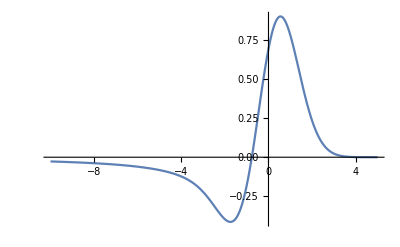

```mathematica
Plot[Asym[z,1.5],{z,-10,5}]
```

```mathematica
Town[z_] = Asym[z,1]
```

ⅇ^(-z^2/2)

```mathematica
SuperTown[z_,a_] = ⅇ^(-z^2/2) Hypergeometric1F1[(1-a)/2,1/2,z^2/2]
```

ⅇ^(-z^2/2) Hypergeometric1F1[(1-a)/2,1/2,z^2/2]

```mathematica
Plot[{Asym[-z,0.5],Town[z],SuperTown[z,1.5]},{z,-10,10}, PlotLabels->"Expressions"]
```

-Graphics-

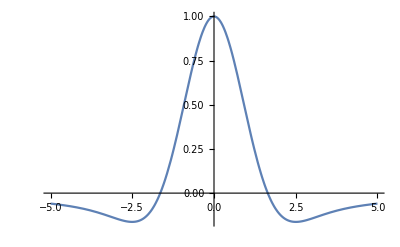

```mathematica
Asymptotic[W[z,a],z->Infinity]
```

-(ⅈ ⅈ^a 2^(1/2-a/2) ⅇ^(-z^2/2) √π z^(-1+a))/Gamma[1/2+1/2 (-1+a)]+(ⅈ^(1+a) 2^(1/2-a/2) ⅇ^(-z^2/2) √π z^(-1+a))/Gamma[1/2+1/2 (-1+a)]+(2^(a/2) √π z^-a)/Gamma[(1-a)/2]

```mathematica
Asymptotic[W[z,1.5],z->Infinity]
```

-0.60814/z^1.5+(0.86004+0.86004 ⅈ) ⅇ^(-z^2/2) z^0.5

```mathematica
Asymptotic[W[z,1],z->Infinity]
```

ⅇ^(-z^2/2)

```mathematica
W[z,1]
```

ⅇ^(-z^2/2)

```mathematica
Asymptotic[Asym[-z,a],z->Infinity]
```

-(2^(a/2) z^-a Gamma[a] Sin[(-1+a) π])/(√π)+ⅈ^a 2^(-3/2+a/2) ⅇ^(-z^2/2) z^(-1+a) (-ⅈ Csc[1/2 (-1+a) π]+Sec[1/2 (-1+a) π]) Sin[(-1+a) π]

```mathematica
Asymptotic[Asym[z,0.5],z->-Infinity]
```

(-7.28179×10^-17-1.18921 ⅈ) (1/z)^0.5-(0.840896+2.12567×10^-16 ⅈ) ⅇ^(-z^2/2) (1/z)^0.5-(2.73067×10^-17+0.445953 ⅈ) (1/z)^2.5